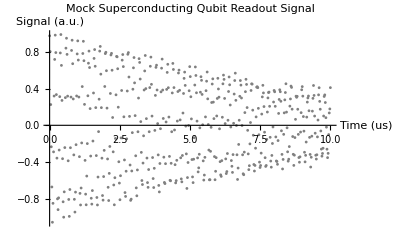

Fisher Information Matrix:

(43374.4 | -148469. | 185.765
-148469. | 809399. | -1857.9
185.765 | -1857.9 | 806692.)

Expected Parameter Uncertainties (CRLB):

{sigma_A→0.00787116,sigma_gamma→0.00182211,sigma_omega→0.00111339}

X::shdw: Symbol X appears in multiple contexts {DifferentialEquations`NDSolveProblems`,Global`}; definitions in context DifferentialEquations`NDSolveProblems` may shadow or be shadowed by other definitions.

Y::shdw: Symbol Y appears in multiple contexts {DifferentialEquations`NDSolveProblems`,Global`}; definitions in context DifferentialEquations`NDSolveProblems` may shadow or be shadowed by other definitions.

RandomVariate::udist: The specification MultivariateNormalDistribution[{0,0,0},{{4.×10^-6,0.,0.},{0.,2.5×10^-7,0.},{0.,0.,0.0001}}] is not a random distribution recognized by the system.

General::stop: Further output of RandomVariate::udist will be suppressed during this calculation.

MCMC Estimated Parameters (Mean +/- Std):

A: 1.02 +/- 0.

gamma: 0.105 +/- 0.

omega: 31.4659 +/- 0.

```mathematica
(*1. Theoretical Signal Model& Parameters*)(*중력파의 파형 모델 h(t;theta)에 해당합니다.*)(*파라미터:A (진폭),gamma (디페이징 rate T2,omega (라비 진동수)*)
signalModel[t_,A_,gamma_,omega_]:=A*Exp[-gamma*t]*Cos[omega*t];

trueA=1.0;
trueGamma=0.1;   (*1/μs*)
trueOmega=2.0*Pi*5.0; (*5 MHz*)
trueParams={trueA,trueGamma,trueOmega};

(*2. Generate Mock Experimental Data*)
(*중력파의 strain 데이터 d(t)=h(t)+n(t) 를 생성하는 과정입니다.*)
tMin=0.0;tMax=10.0;nPoints=500;
tData=Range[tMin,tMax,(tMax-tMin)/(nPoints-1)];

sigmaNoise=0.05; (*Readout Noise Level*)
SeedRandom[1234];  (*Reproducibility*)
mockNoise=RandomVariate[NormalDistribution[0,sigmaNoise],nPoints];
mockSignal=Table[signalModel[t,trueA,trueGamma,trueOmega],{t,tData}];
mockData=mockSignal+mockNoise;

(*Mock Data Plot*)
ListPlot[Thread[{tData,mockData}],PlotStyle->Directive[PointSize[0.005],Gray],Joined->False,PlotLabel->"Mock Superconducting Qubit Readout Signal",AxesLabel->{"Time (us)","Signal (a.u.)"}]

(*3. Fisher Information Matrix (FIM) Calculation*)
(*중력파 파형의 미분값 d_h/d_theta를 계산하여 피셔 행렬을 구하는 핵심 알고리즘입니다.*)
params={A,gamma,omega};
derivatives=Table[D[signalModel[t,A,gamma,omega],p],{p,params}];

(*데이터 지점에서 미분값 산출*)
derivMatrix=Table[derivatives/. {A->trueA,gamma->trueGamma,omega->trueOmega},{t,tData}];

(*Fisher Information Matrix:F_ij=(1/sigma^2)*Sum((dS/d_theta_i)*(dS/d_theta_j))*)
fisherMatrix=(1/sigmaNoise^2)*Transpose[derivMatrix].derivMatrix;

Print["Fisher Information Matrix:"];
Print[MatrixForm[fisherMatrix]];

(*Cramer-Rao Lower Bound (CRLB)-공분산 행렬 (Covariance Matrix)*)
(*중력파의 파라미터 오차 측정 한계 sigma_theta=Sqrt[Cov_ii] 계산과 완벽히 일치합니다.*)
covMatrix=Inverse[fisherMatrix];
paramErrors=Sqrt[Diagonal[covMatrix]];

Print["Expected Parameter Uncertainties (CRLB):"];
Print[Thread[{"sigma_A","sigma_gamma","sigma_omega"}->paramErrors]];

(*4. Bayesian Likelihood& MCMC Sampling*)
(*중력파 LALInference/Bilby 에서 수행하는 posterior P(theta|d) 샘플링 과정입니다.*)
logLikelihood[A_Real,gamma_Real,omega_Real]:=Module[{res},res=mockData-Table[signalModel[t,A,gamma,omega],{t,tData}];
-0.5*Total[res^2]/sigmaNoise^2];

(*Flat Priors*)
logPrior[A_,gamma_,omega_]:=If[0.5<A<1.5&&0.0<gamma<0.5&&2*Pi*4.0<omega<2*Pi*6.0,0.0,-Infinity];
logPosterior[p_List]:=logPrior[p[[1]],p[[2]],p[[3]]]+logLikelihood[p[[1]],p[[2]],p[[3]]];

(*MCMC Sampling (Metropolis-Hastings)*)
Needs["DifferentialEquations`NDSolveProblems`"]; (*Standard Utilities*)
(*간단한 random walk MCMC*)
nMCMC=5000;
samples=ConstantArray[0.0,{nMCMC,3}];
currentP=trueParams+{0.02,0.005,0.05}; (*Initial state slightly off*)
currentLogP=logPosterior[currentP];

Do[proposal=currentP+RandomVariate[MultivariateNormalDistribution[{0,0,0},DiagonalMatrix[{0.002,0.0005,0.01}]^2]];
propLogP=logPosterior[proposal];
If[Log[RandomReal[]]<propLogP-currentLogP,currentP=proposal;
currentLogP=propLogP;];
samples[[i]]=currentP;,{i,1,nMCMC}];

(*Burn-in 제거 및 Posterior 분산 확인*)
postSamples=Drop[samples,1000];
Print["MCMC Estimated Parameters (Mean +/- Std):"];
Print["A: ",Mean[postSamples[[All,1]]]," +/- ",StandardDeviation[postSamples[[All,1]]]];
Print["gamma: ",Mean[postSamples[[All,2]]]," +/- ",StandardDeviation[postSamples[[All,2]]]];
Print["omega: ",Mean[postSamples[[All,3]]]," +/- ",StandardDeviation[postSamples[[All,3]]]];
```